```mathematica
LaunchKernels[10]
```

{Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10),Local (10)}

```mathematica
l=1;
M=1;
μ=M/2;
mpi=1;
α=20;
N0=500; 
qMax=18.00; (*UV Cutoff*)
qGrid=Subdivide[0.001,qMax,N0-1];
Δq=(qMax)/(N0-1);
```

```mathematica
(*Potential Functions: Construct from some V(r) or other..., using convention in the Russian paper*)
V[p_,q_]:=-α/(8*Pi^1.5*mpi)*1/(p*q)*(Exp[-1/(4*mpi^2)*(p-q)^2]-Exp[-1/(4*mpi^2)*(p+q)^2]); (*V(r)=-α e^(-m^2r^2) with l = 0*)
(*V[p_,q_]:=p*q*)
(*V[p_,q_]:=-α*Exp[-1/4*(p+q)^2]*(2+p*q+(p*q-2)*Exp[p*q])/(8p^2*q^2*Pi^1.5); (*V(r)=-α e^(-r^2) with l = 1*)*)
(*V[p_,q_]:=-(α/(16*Pi^1.5*mpi^3))*Exp[-1/(4mpi^2)*(p+q)^2]*(p*q/(2mpi^2))^(-2)(Sinh[p*q/(2mpi^2)]-p*q/(2mpi^2)*Cosh[p*q/(2mpi^2)]); (*V(r)=-α e^(-m^2r^2)*)*)
```

```mathematica
(*Construct the Kernel and inhomogeneous piece*)
gvec[s_]:=4Pi*Table[qGrid[[i]]^2*Δq*1/(s^2-(qGrid[[i]]^2)),{i,N0}];
Vmat=Table[V[qGrid[[i]],qGrid[[j]]],{i,N0},{j,N0}];
Vvec[s_] := Table[V[qGrid[[i]],s],{i,N0}];
Fvec[s_] := Table[I*8*Pi^2*μ*s*V[qGrid[[i]],s]/(1-8*Pi^2*μ*s*V[s,s]),{i,N0}]; (*F as defined in the Russian paper*)
Hmat[s_]:=TensorProduct[Vvec[s],Fvec[s]]; (*Additional term added to kernel for modified LS equation for second sheet*)
Kmat[s_]:=(Vmat+Hmat[s]).DiagonalMatrix[gvec[s]];
```

```mathematica
ResExpr := SetPrecision[Det[IdentityMatrix[N0]-Kmat[s]],20]; (* Calculates Det(1-K)*)

(* Want to sample Det(1-K) in an NxN grid in the 4th quadrant in the k plane (cause thats what corresponds to Im(E)<0), and then check when its close to 0*)
Clear[SampleDetGrid]
SampleDetGrid[Npts_,{xmin_,xmax_},{ymin_,ymax_}]:=Module[{xs,ys},xs=Subdivide[xmin,xmax,Npts-1];
ys=Subdivide[ymin,ymax,Npts-1];
(*Flatten[ParallelTable[{x,y,SetPrecision[Det[IdentityMatrix[N0]-Kmat[x+I*y]],20]},{x,xs},{y,ys}],1];*)
(*skip the origin since its a meaningless pole of K*)
Flatten[ParallelTable[If[x==0&&y==0,Nothing,{x,y,SetPrecision[Det[IdentityMatrix[N0]-Kmat[x+I*y]],20]}],{x,xs},{y,ys}],1] 
];

Npts=100;
{xmin,xmax}={1.3,1.7};
{ymin,ymax}={-1.8,-1.4};

ResGrid =SampleDetGrid[Npts,{xmin,xmax},{ymin,ymax}];
```

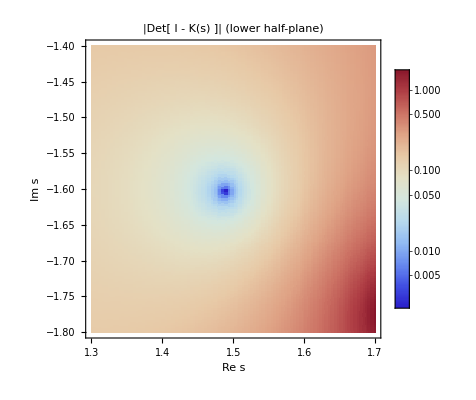

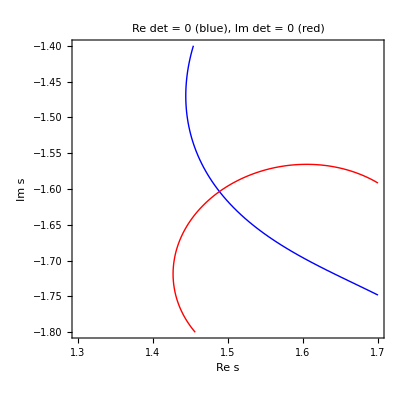

```mathematica
ListDensityPlot[ResGrid/. {x_,y_,v_}:>{x,y,Abs[v]},InterpolationOrder->0,ColorFunction->"ThermometerColors",ScalingFunctions->{"Linear","Linear","Log"},(*log on the color scale only*)FrameLabel->{"Re s","Im s"},PlotLabel->"|Det[ I - K(s) ]| (lower half-plane)",PlotLegends->Automatic]

(*continuous (non-sampled) contour overlay:Re=0 and Im=0 curves*)
detIminusK[s_?NumericQ]:=detIminusK[s]=SetPrecision[Det[IdentityMatrix[N0]-Kmat[s]],20]; (*memoize it so that it runs numerically and 
doesnt symbolically recompute each time*)

detRe[x_?NumericQ,y_?NumericQ]:=Re@detIminusK[x+I y];
detIm[x_?NumericQ,y_?NumericQ]:=Im@detIminusK[x+I y];

(*exclude a tiny disk around s=0 to avoid singular behavior*)
r0=1.*10^-6;

reZero=ContourPlot[detRe[x,y]==0,{x,xmin,xmax},{y,ymin,ymax},RegionFunction->Function[{x,y,v},x^2+y^2>r0^2],PlotPoints->40,MaxRecursion->2,PerformanceGoal->"Speed",ContourStyle->{Thick,Blue}];
imZero=ContourPlot[detIm[x,y]==0,{x,xmin,xmax},{y,ymin,ymax},RegionFunction->Function[{x,y,v},x^2+y^2>r0^2],PlotPoints->40,MaxRecursion->2,PerformanceGoal->"Speed",ContourStyle->{Thick,Red}];

Show[reZero,imZero,FrameLabel->{"Re s","Im s"},PlotLabel->"Re det = 0 (blue), Im det = 0 (red)"]
```